## Pregunta 1

### (1.a)

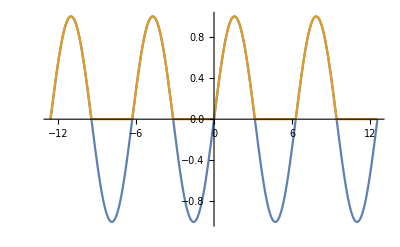

```mathematica
Plot[{Sin[t],1/Pi+Sum[(1+(-1)^n)/(Pi(1-n^2))Cos[n t],{n,2,100}]+1/2 Sin[t]},{t,-4Pi,4Pi}]
```

### (1.b)

```mathematica
Sum[(-1)^m/(4 m^2-1),{m,1,Infinity}]
```

(2-π)/4

```mathematica
N[{Pi/2(1/Pi-1/2),(2-Pi)/4}]
```

{-0.285398,-0.285398}

### (1.c)

```mathematica
Sum[1/((4 m^2-1)^2),{m,1,Infinity}]
```

1/16 (-8+π^2)

## Pregunta 2

### (2.a)

```mathematica
FourierTransform[(UnitStep[t+a]-UnitStep[t-a]),t,w,FourierParameters->{1, -1}]
```

(2 Sin[a w])/w

```mathematica
(*Obtenemos el resultado del problema multiplicando arriba y abajo*)
```

### (2.b)

```mathematica
Integrate[(Sin[a w]/(a w))^2,{w,-Infinity,Infinity}]
```

ConditionalExpression[(π Abs[a])/a^2,a∈Reals]

## Pregunta 3

```mathematica
sumlimit3 = 100;
```

```mathematica
plot3a = Plot[(1-t)(UnitStep[t]-UnitStep[t-2]),{t,-4,4},PlotStyle->{Orange,Thickness[0.008]}];
```

```mathematica
plot3b= Plot[Sum[-I/(n Pi)Exp[n Pi I t],{n,-sumlimit3,-1}]+Sum[-I/(n Pi)Exp[n Pi I t],{n,1,sumlimit3}],{t,-4,4},PlotStyle->{Blue,Thickness[0.01]}];
```

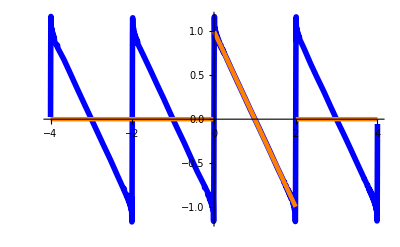

```mathematica
Show[plot3b,plot3a]
```

```mathematica
Table[N[{n,1/(n Pi)}],{n,1,3}]
```

{{1.,0.31831},{2.,0.159155},{3.,0.106103}}

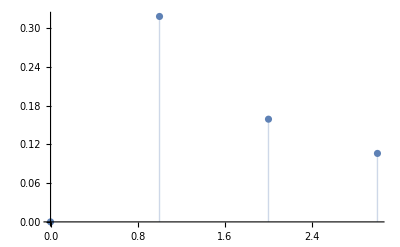

```mathematica
ListPlot[{{0,0},{1.,0.3183098861837907},{2.,0.15915494309189535},{3.,0.1061032953945969}},Filling->Axis]
```

```mathematica
0.9^2/4
```

0.2025

## Pregunta 4

```mathematica
FourierTransform[a(1+a Cos[wc t])Cos[wm t],t,w,FourierParameters->{1, -1}]
```

1/2 a^2 π DiracDelta[w+wc-wm]+a π DiracDelta[-w+wm]+a π DiracDelta[w+wm]+1/2 a^2 π DiracDelta[w-wc+wm]+1/2 a^2 π DiracDelta[-w+wc+wm]+1/2 a^2 π DiracDelta[w+wc+wm]

```mathematica
a=0.5;wc=2000;wm=100;eqn4:= FourierTransform[a(1+a Cos[wm t])Cos[wc t],t,w,FourierParameters->{1, -1}]

(*El como graficar Deltas de Dirac lo agarre de aqui:https://mathematica.stackexchange.com/questions/3506/calling-correct-function-for-plotting-diracdelta
*)
```

```mathematica
ArrowsDeltaFunction[eqn_,x_]:=Module[{xsubs,listDeltas,coefDeltas,locationDeltas},xsubs=(x/.Cases[eqn,DiracDelta[a__]:>Solve[a==0,x],Infinity])/.x->{};
listDeltas=DiracDelta[x-x0]/.x0->xsubs;
coefDeltas=Flatten[Coefficient[eqn,listDeltas]];
locationDeltas=Flatten[xsubs];
Arrow[Table[{{locationDeltas[[i]],0},{locationDeltas[[i]],coefDeltas[[i]]}},{i,1,Length[locationDeltas]}]]]
```

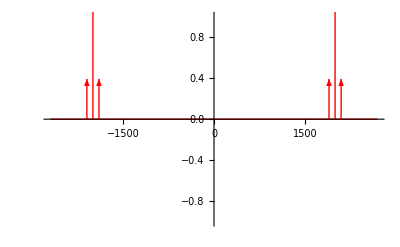

```mathematica
Plot[eqn4,{w,-2700,2700},PlotStyle->{Thick,Red},Epilog->{Thick,Red,ArrowsDeltaFunction[eqn4,w]}]
```

## Pregunta 5

### (5.a)

```mathematica
FourierTransform[1/(1+9 t^2),t,w,FourierParameters->{1, -1}]
```

1/3 ⅇ^(-Abs[w]/3) π

### (5.b)

```mathematica
FourierTransform[t Exp[-1/2(t-1)^2],t,w,FourierParameters->{1, -1}]
```

ⅇ^(-1/2 w (2 ⅈ+w)) √(2 π) (1-ⅈ w)